```mathematica
Get[FileNameJoin[{NotebookDirectory[],"sgemm_plot.m"}]]
```

no_plot.png

```mathematica
Dataset[groupedData]
```

BarChart::ldata: <|{Missing[KeyAbsent,bytes]}→{<|name→SGEMM/1000/1/1,iterations→193040,real_time→3649.4,cpu_time→3651.72,time_unit→ns,K→1.,M→1000.,N→1.,machine→Whatever_with_smt|>,<|name→SGEMM/128/169/1728,iterations→1308,real_time→444289.,cpu_time→444175.,time_unit→ns,K→1728.,M→128.,N→169.,machine→Whatever_with_smt|>,«267»,<|name→SGEMM/1024/4/512,iterations→2183,real_time→311158.,cpu_time→311156.,time_unit→ns,K→512.,M→1024.,N→4.,machine→Whatever_with_smt_updated|>},«31»,{4.29497×10^9}→«1»|> is not a valid dataset or list of datasets.

BarChart[<|{Missing[KeyAbsent,bytes]}→{<|name→SGEMM/1000/1/1,iterations→193040,real_time→3649.4,cpu_time→3651.72,time_unit→ns,K→1.,M→1000.,N→1.,machine→Whatever_with_smt|>,268,<|name→SGEMM/1024/4/512,iterations→2183,real_time→311158.,cpu_time→311156.,time_unit→ns,K→512.,M→1024.,N→4.,machine→Whatever_with_smt_updated|>},{2.}→{<|1|>,1},29,1,{4.29497×10^9}→{<|name→CUDAMemcpyToGPU/32,iterations→2,4,bytes→4.29497×10^9,machine→Minsky_pageable|>,<|1|>}|>]
 |  |  |  |

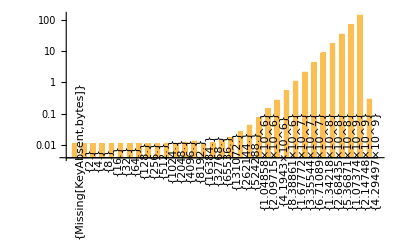

```mathematica
data=Take[groupedData,UpTo[100]];
BarChart[Association[SortBy[KeyValueMap[Function[{key,val},key->AssociationThread[Lookup[val,"key"]->Lookup[val,"cpu_time"]/10^6]],data],Fold[Times,1,First[#]]&]],ChartLabels->{Placed[Keys[data],Automatic,Rotate[#,90Degree]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,1},PlotTheme->"Grid",ScalingFunctions->"Log"]
```

```mathematica
makeChart[data_]:=BarChart[Association[SortBy[KeyValueMap[Function[{key,val},key->AssociationThread[Lookup[val,"key"]->Lookup[val,"cpu_time"]/10^6]],data],Fold[Times,1,First[#]]&]],ChartLabels->{Placed[Keys[data],Automatic,Rotate[#,90 Degree]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,1},PlotTheme->"Grid",ScalingFunctions->"Log"];
```

```mathematica
makeChart[data]
```

-Graphics-

```mathematica
2560*7680*1500
```

29491200000

```mathematica
Dataset[groupedData[{500000.0,512.0,1.0}]]
```

Dataset[<>]

## AMD64 Speedup by turning off SMT

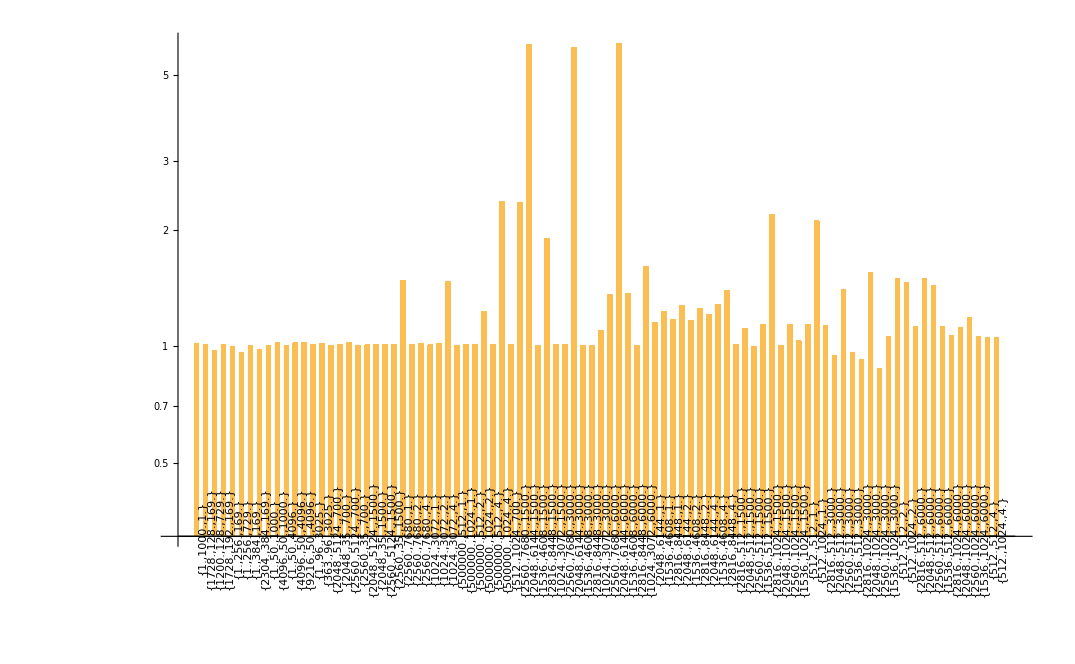

```mathematica
data=Take[groupedData,UpTo[100]];
divide[{a_,b_}]:=a/b;
BarChart[Association[SortBy[KeyValueMap[Function[{key,val},key-><|"Speedup"->divide[Lookup[val,"cpu_time"]]|>],data],Fold[Times,1,First[#]]&]],ChartLabels->{Placed[Keys[data],Automatic,Rotate[#,90Degree]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,1},PlotTheme->"Grid",ScalingFunctions->"Log"]
```

## Minsky Speedup by turning off SMT

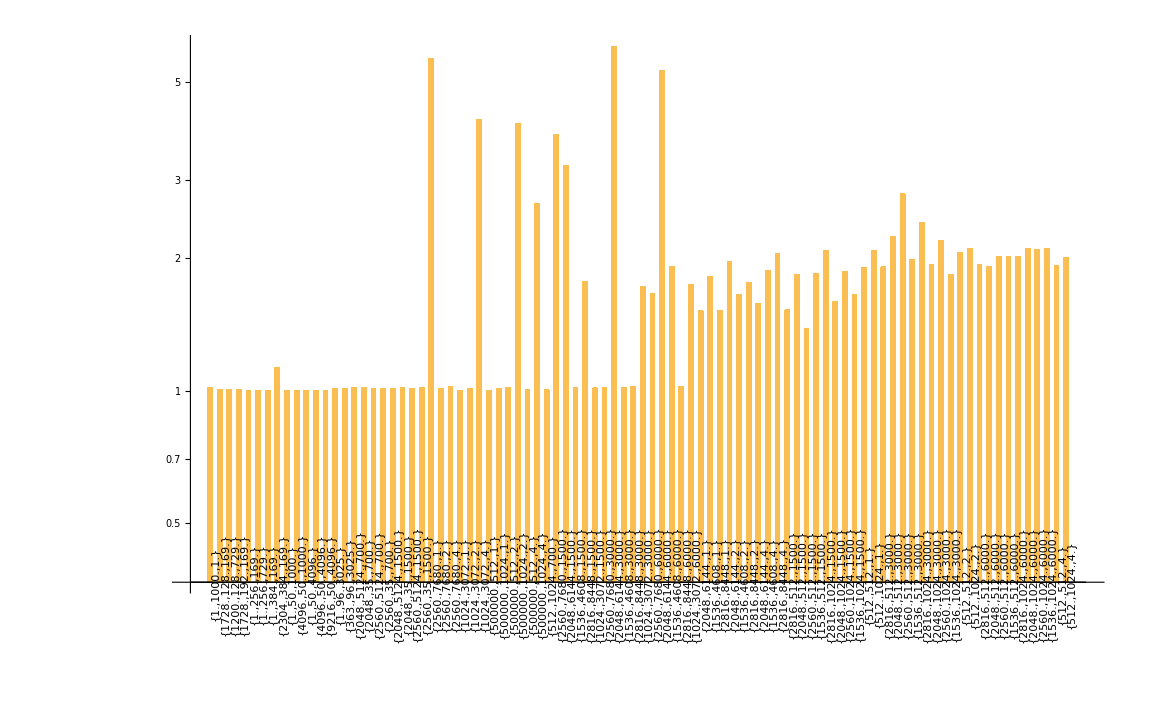

```mathematica
data=Take[groupedData,UpTo[100]];
divide[{a_,b_}]:=a/b;
BarChart[Association[SortBy[KeyValueMap[Function[{key,val},key-><|"Speedup"->divide[Lookup[val,"cpu_time"]]|>],data],Fold[Times,1,First[#]]&]],ChartLabels->{Placed[Keys[data],Automatic,Rotate[#,90Degree]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,1},PlotTheme->"Grid",ScalingFunctions->"Log"]
```